```mathematica
(*P+P-N+ TFET*)
```

```mathematica
Tsi=10*10^-9;
Tox=1.45*10^-9;
W=1*10^-6;
q=1.6*10^-19;
Eg=0.74*q;
Ns=5*10^25;
Nch=1*10^18;
ni=6.3*10^17;
m0=9.1*10^-31;
me=0.016*m0;
mdos=0.4*m0;
eps0=8.85*10^-12;
epsox=3.9;
epsch=13.9;
epss=13.9;
hbar=6.626*10^-34/(2*π);
Vt=0.026;
eaff=4.5*q;
Nv=6.575*10^24;
Wfg=4.52*q;
Ws=If[Ns/Nv≥ⅇ^-3,((3*√π)/4*Ns/Nv)^(2/3)*Vt*q+Eg+eaff,eaff+Eg/2+q*Vt*Log[Ns/ni]];
Wch=eaff+Eg/2+q*Vt*Log[Nch/ni];
Vfbs=(Wfg-Ws)/q;
Vfbb=(Wfg-Wch)/q;
Cox=epsox*eps0/Tox;
phif=2*q*Vt*Log[Nch/ni];
Vbis=Vt*Log[Ns/Nch];
lambda1=√(epss*eps0*Tsi*(Tox*π/2)/(2*epsox*eps0));
lambda2=√(epsch*eps0*Tsi*Tox/(2*epsox*eps0));
Nseff[x_]:=2*(epss*eps0)/q*((q*Ns)/(2*epss*eps0)-epsox/epss*(x-Vfbs)/Tox*(Tsi*π)/2);
phi[x_]:=(q*Nseff[x]*lambda2*lambda2)/(epss*eps0);
phidg[x_]:=(q*Nch*epsch*eps0)/(2*Cox^2)(√(1+(2*Cox^2*(x-Vfbb))/(q*Nch*epsch*eps0))-1)^2;
phidg1[x_]:=phidg[x]/((1+(phidg[x]/1.0)^4)^(1/4));
phis0[x_]:=-√((x-Vfbs-Vbis-phidg1[x])^2+2*(x-Vfbs)*phi[x]+phi[x]^2)+(x-Vfbs+phi[x]);
L2[x_]:=lambda2*ArcCosh[(x-Vfbs-phis0[x])/(x-Vfbs-Vbis-phidg1[x])];
L1[x_]:=√((2*epss*eps0*phis0[x])/(q*Nseff[x]));
eta[x_,y_]:=√q*√(1/2(x-Vfbs-Vbis-phidg1[x])*ⅇ^(L2[x]/lambda2)-(x-Vfbs)+y);
eta0[x_,y_]:=√q*√((x-Vfbs-Vbis-phidg1[x])*Cosh[L2[x]/lambda2]-(x-Vfbs)+y);
eta1[x_,y_]:=√q*√((x-Vfbs)-y);
T[x_,y_]:=If[y≤phis0[x]&&y≥Eg/q,Exp[-(4*lambda2*√(2*me))/hbar*(eta0[x,y]-eta1[x,y]*ArcTan[eta0[x,y]/eta1[x,y]])],Exp[-(4*lambda2*√(2*me))/hbar*(√Eg-eta1[x,y]*ArcTan[(√Eg)/eta1[x,y]])]];
T2[x_,y_]:=Which[y≥0&&y≤phis0[x],Exp[(-2*√(2*me))/hbar*(1/2*(L1[x]*√(-y*q+(q*q*Nseff[x])/(2*epss*eps0)*L1[x]*L1[x])-(y*q*Log[(q*q*Nseff[x])/(2*epss*eps0)*L1[x]+√((q*q*Nseff[x])/(2*epss*eps0))*√(-y*q+(q*q*Nseff[x])/(2*epss*eps0)*L1[x]*L1[x])])/(√((q*q*Nseff[x])/(2*epss*eps0))))+(y*q*Log[(q*q*Nseff[x])/(2*epss*eps0)*√((2*epss*eps0*y*q)/(q*q*Nseff[x]))])/(2*√((q*q*Nseff[x])/(2*epss*eps0))))],y≥phis0[x],1,y≤0,0];
M[y_]:=W*1*(√(2*mdos*(y*q-Eg)))/(π*hbar);
Id[x_,z_?NumericQ]:=If[Vbis+phidg1[x]≥Eg/q,NIntegrate[(2*2*q*q)/(hbar*2*π)*M[y]*(1/(1+ⅇ^(((Ws-eaff)/q-y)/Vt))-1/(1+ⅇ^(((Ws-eaff)/q+z-y)/Vt)))*T[x,y]*T2[x,y-Eg/q],{y,Eg/q,Vbis+phidg1[x]},MinRecursion->9],10^-21]
dId[x_,y_,z_]:=If[Vbis+phidg1[x]≥Eg/q,(2*2*q*q)/(hbar*2*π)*M[y]*(1/(1+ⅇ^(((Ws-eaff)/q-y)/Vt))-1/(1+ⅇ^(((Ws-eaff)/q+z-y)/Vt)))*T[x,y]*T2[x,y-Eg/q],MinRecursion->9,10^-21];
BA1[x_]:=Vbis+phidg1[x]-Eg/q;
BA2[x_]:=Vbis+phidg1[x]+Eg/q;
GI[vg_,vd_]:=If[Vbis+phidg1[vg]≥Eg/q,dId[vg,(BA1[vg]*0.0697392733197222+BA2[vg])/2,vd]*BA1[vg]/2*0.1392518728556320+dId[vg,(BA1[vg]*(-0.0697392733197222)+BA2[vg])/2,vd]*BA1[vg]/2*0.1392518728556320+dId[vg,(BA1[vg]*0.2078604266882213+BA2[vg])/2,vd]*BA1[vg]/2*0.1365414983460152+dId[vg,(BA1[vg]*(-0.2078604266882213)+BA2[vg])/2,vd]*BA1[vg]/2*0.1365414983460152+dId[vg,(BA1[vg]*0.3419358208920842+BA2[vg])/2,vd]*BA1[vg]/2*0.1311735047870624+dId[vg,(BA1[vg]*(-0.3419358208920842)+BA2[vg])/2,vd]*BA1[vg]/2*0.1311735047870624+dId[vg,(BA1[vg]*0.4693558379867570+BA2[vg])/2,vd]*BA1[vg]/2*0.1232523768105124+dId[vg,(BA1[vg]*(-0.4693558379867570)+BA2[vg])/2,vd]*BA1[vg]/2*0.1232523768105124+dId[vg,(BA1[vg]*0.5876404035069116+BA2[vg])/2,vd]*BA1[vg]/2*0.1129322960805392+dId[vg,(BA1[vg]*(-0.5876404035069116)+BA2[vg])/2,vd]*BA1[vg]/2*0.1129322960805392+dId[vg,(BA1[vg]*0.6944872631866827+BA2[vg])/2,vd]*BA1[vg]/2*0.1004141444428810+dId[vg,(BA1[vg]*(-0.6944872631866827)+BA2[vg])/2,vd]*BA1[vg]/2*0.1004141444428810+dId[vg,(BA1[vg]*0.7878168059792081+BA2[vg])/2,vd]*BA1[vg]/2*0.0859416062170677+dId[vg,(BA1[vg]*(-0.7878168059792081)+BA2[vg])/2,vd]*BA1[vg]/2*0.0859416062170677+dId[vg,(BA1[vg]*0.8658125777203002+BA2[vg])/2,vd]*BA1[vg]/2*0.0697964684245205+dId[vg,(BA1[vg]*(-0.8658125777203002)+BA2[vg])/2,vd]*BA1[vg]/2*0.0697964684245205+dId[vg,(BA1[vg]*0.9269567721871740+BA2[vg])/2,vd]*BA1[vg]/2*0.0522933351526833+dId[vg,(BA1[vg]*(-0.9269567721871740)+BA2[vg])/2,vd]*BA1[vg]/2*0.0522933351526833+dId[vg,(BA1[vg]*0.9700604978354287+BA2[vg])/2,vd]*BA1[vg]/2*0.0337749015848142+dId[vg,(BA1[vg]*(-0.9700604978354287)+BA2[vg])/2,vd]*BA1[vg]/2*0.0337749015848142+dId[vg,(BA1[vg]*0.9942945854823992+BA2[vg])/2,vd]*BA1[vg]/2*0.0146279952982722+dId[vg,(BA1[vg]*(-0.9942945854823992)+BA2[vg])/2,vd]*BA1[vg]/2*0.0146279952982722,10^-21];
DataSat=Table[{vg,GI[vg,0.3]},{vg,-0.1,0.4,0.01}];
DataLin=Table[{vg,GI[vg,0.05]},{vg,0,1.2,0.01}];
Data02=Table[{vd,GI[0.2,vd]},{vd,0,1,0.01}];
Data04=Table[{vd,GI[0.4,vd]},{vd,0,1,0.01}];
Data06=Table[{vd,GI[0.6,vd]},{vd,0,1,0.01}];
Data08=Table[{vd,GI[0.8,vd]},{vd,0,1,0.01}];
Data1=Table[{vd,GI[1,vd]},{vd,0,1,0.01}];
IntelInGaAsData0p3={{1.2,6*10^-6},{1.1,5.5*10^-6},{1.0,5*10^-6},{0.9,4*10^-6},{0.8,2.5*10^-6},{0.7,1.2*10^-6},{0.6,6*10^-7},{0.5,1.6*10^-7},{0.4,4*10^-8},{0.3,2*10^-9},{0.2,1.5*10^-10},{0.1,6*10^-11}};
IntelInGaAsData0p05={{1.2,4*10^-7},{1.1,3.5*10^-7},{1.0,3*10^-7},{0.9,1.8*10^-7},{0.8,1.5*10^-7},{0.7,8.5*10^-8},{0.6,5*10^-8},{0.5,2*10^-8},{0.4,7*10^-9},{0.3,1*10^-9},{0.2,1.2*10^-10},{0.1,2*10^-11}};
IntelGaSbInAsData0p3={{0.4,1.7*10^-4},{0.3,1*10^-4},{0.2,3*10^-5},{0.1,5*10^-6},{0.0,7*10^-8},{-0.1,3*10^-9}};
```

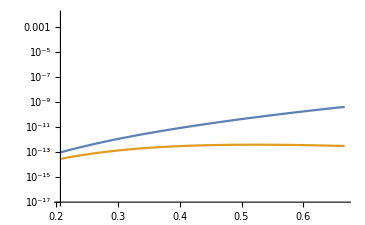

```mathematica
LogPlot[{Id[x,1],Id[x,0.05]},{x,0,1},PlotRange->{10^-17,10^-2}]
```

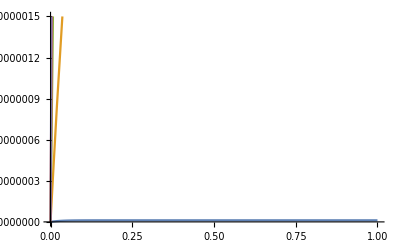

```mathematica
Plot[{Id[0.2,z],Id[0.4,z],Id[0.6,z],Id[0.8,z],Id[1,z]},{z,0,1},PlotRange->{0,1.5*10^-6}]
```

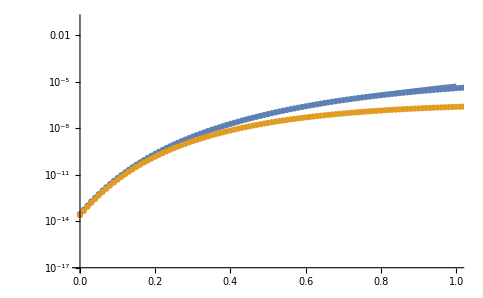

```mathematica
Show[LogPlot[{Id[vg,1],Id[vg,0.05]},{vg,0,1},PlotRange->{10^-17,10^-1}],ListLogPlot[{DataSat,DataLin}]]
```

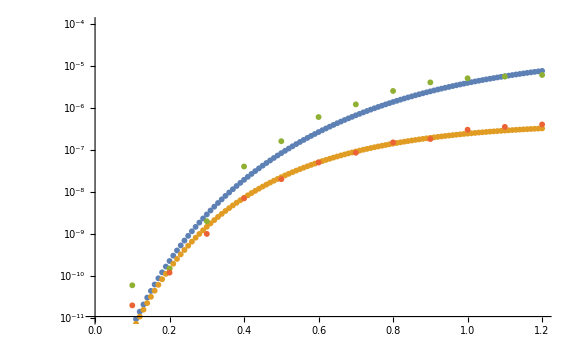

```mathematica
ListLogPlot[{DataSat,DataLin,IntelInGaAsData0p3,IntelInGaAsData0p05},PlotRange->{10^-11,10^-4}]
```

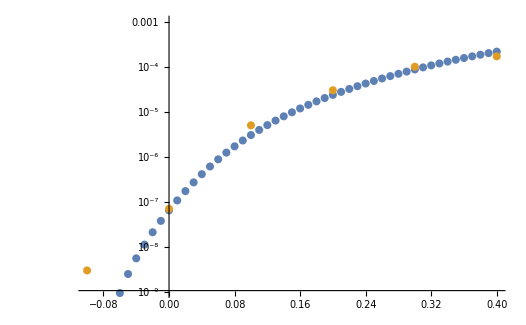

```mathematica
ListLogPlot[{DataSat,IntelGaSbInAsData0p3},PlotRange->{10^-9,10^-3}]
```

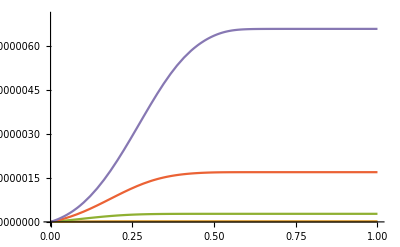

```mathematica
Plot[{GI[0.2,vd],GI[0.4,vd],GI[0.6,vd],GI[0.8,vd],GI[1,vd]},{vd,0,1},PlotRange->{0,7*10^-6}]
```

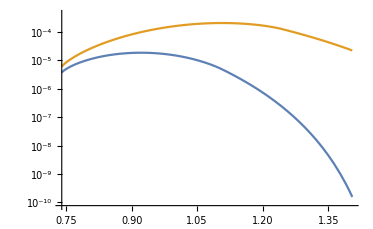

```mathematica
LogPlot[{T[0.6,y]*T2[0.6,y-Eg/q],T[1,y]*T2[1,y-Eg/q]},{y,Eg/q,Vbis+phidg1[1]}]
```

```mathematica
Export["GIsat_Si.txt",DataSat,"Table"];
Export["GIlin_Si.txt",DataLin,"Table"];
Export["GIIdVd02_Si.txt",Data02,"Table"];
Export["GIIdVd04_Si.txt",Data04,"Table"];
Export["GIIdVd06_Si.txt",Data06,"Table"];
Export["GIIdVd08_Si.txt",Data08,"Table"];
Export["GIIdVd1_Si.txt",Data1,"Table"];
```

```mathematica
NumericalSat=Table[{vg,Id[vg,1]},{vg,0,1,0.01}];
NumericalLin=Table[{vg,Id[vg,0.05]},{vg,0,1,0.01}];
Numerical02=Table[{vd,Id[0.2,vd]},{vd,0,1,0.01}];
Numerical04=Table[{vd,Id[0.4,vd]},{vd,0,1,0.01}];
Numerical06=Table[{vd,Id[0.6,vd]},{vd,0,1,0.01}];
Numerical08=Table[{vd,Id[0.8,vd]},{vd,0,1,0.01}];
Numerical1=Table[{vd,Id[1,vd]},{vd,0,1,0.01}];
Export["NIsat_Si.txt",NumericalSat,"Table"];
Export["NIlin_Si.txt",NumericalLin,"Table"];
Export["NIIdVd02_Si.txt",Numerical02,"Table"];
Export["NIIdVd04_Si.txt",Numerical04,"Table"];
Export["NIIdVd06_Si.txt",Numerical06,"Table"];
Export["NIIdVd08_Si.txt",Numerical08,"Table"];
Export["NIIdVd1_Si.txt",Numerical1,"Table"];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

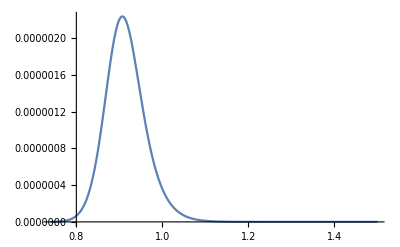

```mathematica
Plot[(2*2*q*q)/(hbar*2*π)*M[y]*(1/(1+ⅇ^(((Ws-eaff)/q-y)/Vt))-1/(1+ⅇ^(((Ws-eaff)/q+0.05-y)/Vt)))*T[1,y]*T2[1,y-Eg/q],{y,Eg/q,1.5}]
```